### Categorization

Tutorial

Wolfram/QuantumFramework

Wolfram`QuantumFramework`

Wolfram/QuantumFramework/tutorial/GettingStarted

### Keywords

# Getting Started

How to install and load the paclet

Install the paclet and load it:

```mathematica
PacletInstall["Wolfram/QuantumFramework"]
Needs["Wolfram`QuantumFramework`"]
```

PacletObject[…]

Check whether definitions are now available:

```mathematica
Names["Quantum*"]
```

{QuantumBasis,QuantumChannel,QuantumCircuitOperator,QuantumDiagramProcess,QuantumDistance,QuantumEntangledQ,QuantumEntanglementMonotone,QuantumLabelName,QuantumMeasurement,QuantumMeasurementOperator,QuantumOperator,QuantumPartialTrace,QuantumPartialTranspose,QuantumState,QuantumStateEstimate,QuantumStateEstimation,QuantumStateSampler,QuantumTensorProduct,QuantumWignerTransform}

A quantum gate for the magic basis transformation (transforming 2 qubit computational basis to the Bell basis):

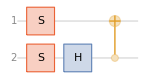

```mathematica
qc=QuantumCircuitOperator["Magic"];
qc["Diagram"]
```

Test how above circuit transforms computational basis of 2-qubit into Bell states:

```mathematica
qc[QuantumState["00"]]==QuantumState["PhiPlus"]
```

True

```mathematica
qc[QuantumState["10"]]==ⅈ QuantumState["PsiPlus"]
```

True

```mathematica
qc[QuantumState["01"]]==ⅈ QuantumState["PhiMinus"]
```

True

```mathematica
qc[QuantumState["11"]]== QuantumState["PsiMinus"]
```

True

Generate corresponding tensor network of the circuit

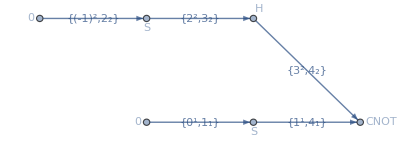

```mathematica
qc["TensorNetwork",EdgeLabels->Automatic]
```

Add measurements into above circuit

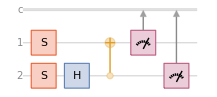

```mathematica
qc2={{1},{2}}@*qc;
qc2["Diagram"]
```

Calculate the result of circuit on registered state:

```mathematica
mea=qc2[]
```

QuantumMeasurement[…]

Represents the corresponding probabilities:

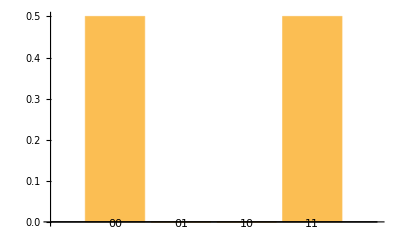

```mathematica
mea["ProbabilityPlot"]
```

Related Guides

Related Tech Notes